The analytical way!

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Here we solve for the roots of the sixth-order polynomial *)
Subscript[rootEq, k_][r_,Ra_]:=-k^-2(r^2-k^2)^3==Ra;
roots=r/.Solve[Subscript[rootEq, k][r,Ra],r];

(* Here we define the six basis functions *)
bfuns=Table[Exp[roots⟦i⟧z],{i,Length[roots]}]//FullSimplify;

(* Here we define the six boundary conditions given a function *)
bcs[f_,z_,vs_]:={f/.{z->vs⟦1⟧},f/.{z->vs⟦2⟧},
Evaluate[D[f,{z,2}]-k^2 f]/.{z->vs⟦1⟧},
Evaluate[D[f,{z,2}]-k^2 f]/.{z->vs⟦2⟧},
Evaluate[D[f,{z,3}]-k^2 D[f,z]]/.{z->vs⟦1⟧},
Evaluate[D[f,{z,3}]-k^2 D[f,z]]/.{z->vs⟦2⟧}};

(* Here we construct the matrix as described *)
vmond=Table[bcs[bfuns⟦i⟧,z,{0,1}],{i,6}]//Transpose;
```

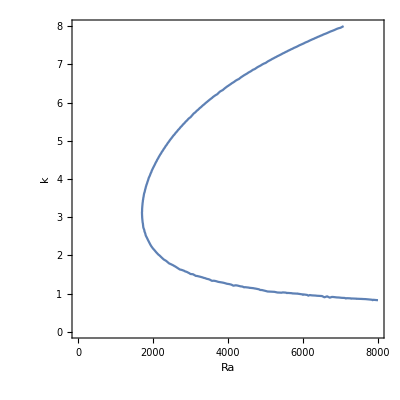

```mathematica
(* Here we plot the contour of det(M) = 0 (technically Im(det)=0) *)
c=ContourPlot[If[2k<Ra^(1/3),Im[Det[vmond]],10]==0,{Ra,0,8000},{k,0,8},Frame->True,FrameStyle->Directive[Black,14],FrameLabel->{"Ra","k"}]
```

We can also zoom in and grab the leftmost point from it.

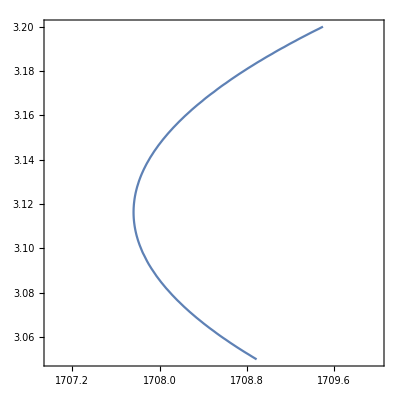

```mathematica
c=ContourPlot[If[2k<Ra^(1/3),Im[Det[vmond]],10]==0,{Ra,1707,1710},{k,3.05,3.2}]
```

```mathematica
(* this pulls out the leftmost point on the contour *)
ord=Ordering[c⟦1,1⟧⟦;;,1⟧];
c⟦1,1⟧⟦ord⟦1⟧⟧
```

{1707.76,3.11621}

```mathematica
ClearAll["Global`*"]
```

The shooting method way!

```mathematica
(* Here we define the differential operator of the
Laplacian and use it to define the operater Subscript[D, k] *)
Subscript[lap, k_][f_,z_]:=D[f,{z,2}]-k^2 f;
Subscript[eq, k_][f_,z_,λ_]:=-k^-2 Subscript[lap, k][Subscript[lap, k][Subscript[lap, k][f,z],z],z]==λ f //FullSimplify;

(* Here we define expressions for the six boundary conditions *)
Subscript[lap, k_][f_,v_,z_]:=(Evaluate[Subscript[lap, k][f,z]]/.{z->v});
Subscript[bcs, k_][g_]:={g[0]==0,g'[0]==1,
Subscript[lap, k][g[z],0,z]==0,
Subscript[lap, k][g[z],1,z]==0,
Subscript[lap, k][g'[z],0,z]==0,
Subscript[lap, k][g'[z],1,z]==0};
```

Some useful functions...

```mathematica
(* this does the numerical integration (shoots from x=0)
for a given k and Ra *)
sol[kk_,Ra_]:=NDSolve[Evaluate[Join[{Subscript[eq, k][h[x],x,λ]},Subscript[bcs, k][h]]]/.{k->kk,λ->Ra},h,{x,0,1}];

(* these are a residual function (i.e. how much we miss by at x = 1
at a given k and Ra) and representation of the obtained function itself *)
res[k_,Ra_]:=h[1]/.sol[k,Ra]⟦1⟧;
fun[k_,Ra_]:=h/.sol[k,Ra]⟦1⟧;
```

Here are some figures, trying out different Ra’s for k = 3.1.

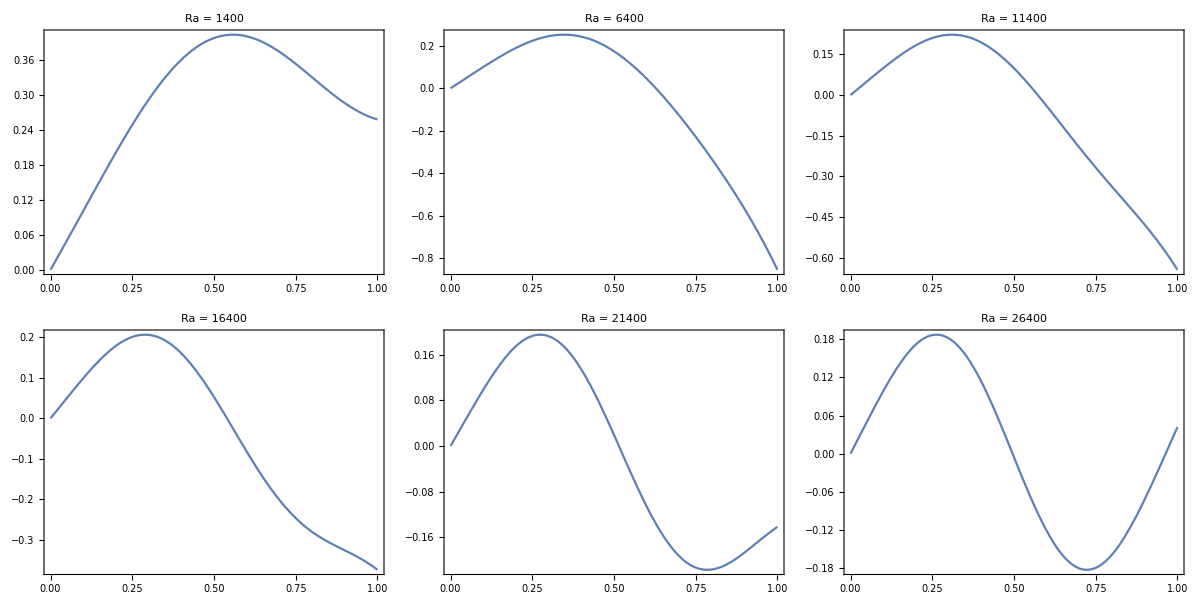

```mathematica
Table[Module[{f},f=fun[3.1,Ra];Plot[f[x],{x,0,1},PlotLabel->StringForm["Ra = ``",Ra],Frame->True,FrameStyle->Directive[Black,14]]],{Ra,1400,30000,5000}];
Grid[{%⟦1;;3⟧,%⟦4;;⟧}]
```

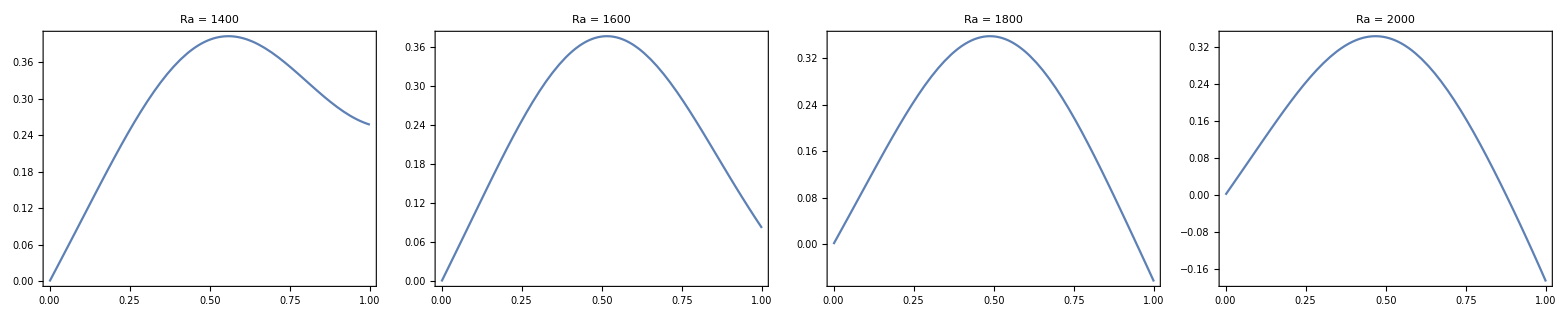

```mathematica
Grid[{Table[Module[{f},f=fun[3.1,Ra];Plot[f[x],{x,0,1},PlotLabel->StringForm["Ra = ``",Ra],Frame->True,FrameStyle->Directive[Black,14]]],{Ra,1400,2000,200}]}]
```

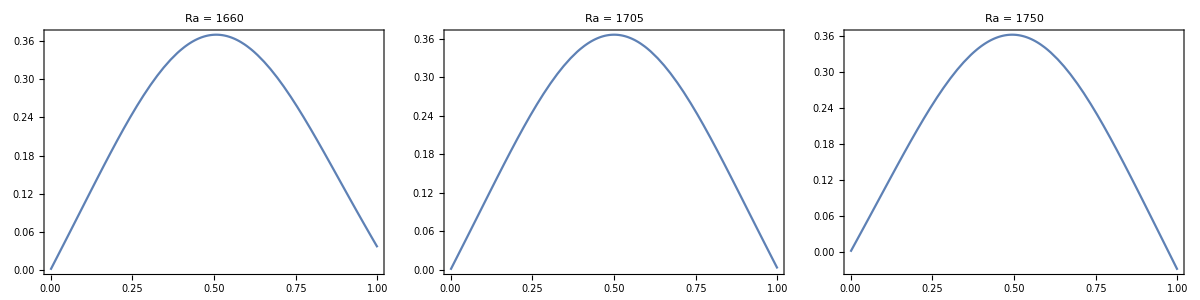

```mathematica
Grid[{Table[Module[{f},f=fun[3.1,Ra];Plot[f[x],{x,0,1},PlotLabel->StringForm["Ra = ``",Ra],Frame->True,FrameStyle->Directive[Black,14]]],{Ra,1660,1770,45}]}]
```

```mathematica
(* this is a function to apply the bisection method to find
the zero of a function *)
bis[k_,rlow_,rhi_,tol_,f_]:=Module[{a,b,m,ra,rb,rm},
ra=rlow;
rb=rhi;
While[rb-ra>tol,
rm=(ra+rb)/2//N;
a=f[ra];
b=f[rb];
m=f[rm];
If[a m<0,
rb=rm,ra=rm];
];
rm];
```

```mathematica
(* this finds the minimum ra for a given k by applying the
bisection method above to find the zero of f(1) as a
function of the Rayleigh number *)
ra[k_]:=Module[{x,g},
g[x_]:=res[k,x];
bis[k,1000,2000,0.0001,g]]
```

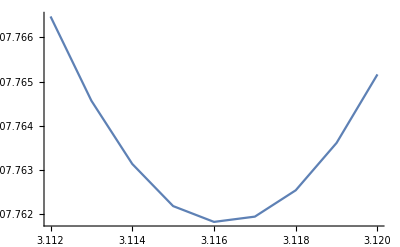

```mathematica
(* here we plot Ra(k), obtained using the function above,
which shows a minimum at the critical k *)
dat=Monitor[Table[{kk,ra[kk]},{kk,3.112,3.12,0.001}],kk];
ListLinePlot[dat]
```

```mathematica
(* and we can print out the min values, which look pretty good *)
ord=Ordering[dat⟦;;,2⟧];
dat⟦ord⟦1⟧⟧
```

{3.116,1707.76}

```mathematica
ClearAll["Global`*"]
```

The matrix way!

```mathematica
(* functions to build operator with *)
eye[n_]:=IdentityMatrix[n];
ones[n_]:=Table[1,{i,n}];
zeros[n_]:=Table[0,{i,n}];

(* a second derivative matrix *)
d2[n_,Δ_]:=1/Δ^2(DiagonalMatrix[ones[n-1],-1]+DiagonalMatrix[ones[n-1],1]-2eye[n]);

(* the laplacian is the second derivative minus k^2 *)
lap[k_,n_,Δ_]:=d2[n,Δ]-k^2 eye[n];

(* this builds the relevant operator. We need to add some
rows and cols to the laplacian matrix before multiplying
and then pick them off - otherwise, we're not recovering the
correct stencils at the first three points on each side *)
M[k_,n_]:=Module[{mat},
mat=-k^-2 MatrixPower[lap[k,n+10,1/n],3];
mat⟦6;;-6,6;;-6⟧
];

(* finally, here's a function for pulling the stencil out of a
matrix by grabbing a row in the middle and trimming zeros from
either side of it *)
sten[vec_,v_]:=(vec/.{Longest[v...],x___}:>{x})/.{x___,v...}:>{x};
sten[mat_]:=sten[sten[mat⟦Length[mat]/2⟧,0],0.];
```

```mathematica
(* this produces a 3x3 matrix defining the linear relationship between
the three ghost nodes and first three real nodes so that an interpolant
satisfies our boundary conditions *)
nodeRels[k_,Δ_]:=Module[{c0,c1,c2,c3,c4,c5,f,sol,h0,h1,h2,pts},
f[x_]:=c5 x^5+c4 x^4+c3 x^3+c2 x^2+c1 x^1+c0;
sol=Solve[{f'''[0]==k^2 f'[0],f''[0]==k^2 f[0],f[0]==0,
f[Δ/2]==h0,f[(3Δ)/2]==h1,f[(5Δ)/2]==h2},{c0,c1,c2,c3,c4,c5}];
pts=(f[x]/.sol⟦1⟧)/.{x->{-(5Δ)/2,-(3Δ)/2,-Δ/2}};
Transpose[{D[pts,h0],D[pts,h1],D[pts,h2]}//FullSimplify]]
```

```mathematica
(* this updates the matrix coefficients to reflect the application
of the stencil to the ghost nodes, given the relations above *)
applyBCs[mat_,k_]:=Module[{n,nrs,st,mat2,stt},
n=Length[mat];
nrs=nodeRels[k,1/n];
st=sten[mat];
mat2=mat;
Do[stt=Join[zeros[r-1],st⟦1;;4-r⟧];

mat2⟦r,1;;3⟧=mat2⟦r,1;;3⟧+stt.nrs,{r,1,3}];
Do[stt=Join[zeros[n-r],st⟦1;;3-n+r⟧];

mat2⟦r,(n-2);;n⟧=mat2⟦r,(n-2);;n⟧+Reverse[stt.nrs],{r,n-2,n}];
mat2
]
```

```mathematica
(* This takes a given k and N points, constructs the system,
and returns the eigenvals and vecs *)
sys[k_,n_,bc_]:=Module[{evals,evecs,ord,mat},
mat=If[bc,applyBCs[M[k,n],k],M[k,n]]//N;
{evals,evecs}=Eigensystem[mat];
ord=Ordering[evals];
evals=evals⟦ord⟧;
evecs=Re[evecs⟦ord⟧];
evecs=Table[Join[{{0,0}},Table[{(ii-0.5)/n,evecs⟦i⟧⟦ii⟧},{ii,n}],{{1,0}}],{i,n}] ;
{evals,evecs}]
```

```mathematica
(* this constructs plots of the first m eigenvectors *)
plots[sys_,m_]:=
ListLinePlot[s⟦2⟧⟦1;;m⟧,PlotLegends->Table[StringForm["Ra = ``",s⟦1⟧⟦i⟧],{i,m}],FrameLabel->{"z","f(z)"},Frame->True,
FrameStyle->Directive[Black,14]]
```

```mathematica
(* this takes in a k and returns the Ra of the lowest mode *)
raMin[k_,bc_]:=Module[{s},
s=sys[k,100,bc];
s⟦1⟧⟦1⟧]
```

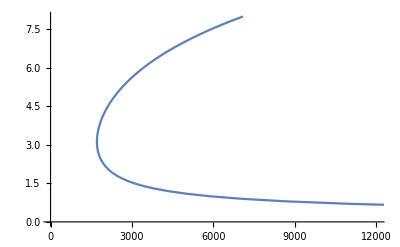

```mathematica
(* plotting this Ra(k) matches the contour from the analytical section *)
ListLinePlot[Table[{raMin[k,True],k},{k,0.1,8,0.1}]]
```

```mathematica
(* We can sift through ra(k) to find the minimum value *)
raVals=Table[{k,raMin[k,True]},{k,3,4,0.001}];
raVals⟦Ordering[raVals⟦;;,2⟧]⟦1⟧⟧
```

{3.116,1707.63}

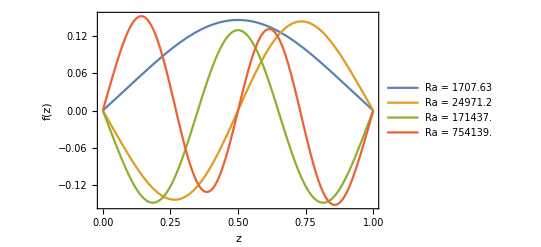

```mathematica
(* plots from the writeup *)
s=sys[3.116,100,True];
plots[s,4]
```